# Sequence Network Connectivity Analysis

For an associative net between A and B patterns, we consider A's and B's of N dimensions, with M_A and M_B neurons randomly picked for each A and B to fire.  Hence there are N^2 total points in this associative net, which we may call C.

We may regard an A-pattern as a prior-pattern and a B-pattern as an after-pattern in the sequence network.  Coincidence in firing between the two patterns lead to a filled element in the connectivity (or weight) matrix.

The question we ask is, after R pairs of A-B are present, what is the probability that an element in the N-by-N connectivity matrix (associative net) is not filled?

We begin by declaring that P(R) is the probability that a certain point of the net is not filled after R pairs of A-B.  From the assumption of randomly generaged A's and B's, similar to those made for Poisson processes, we have

P(R+dR) = P(R) P(dR),

where we take the continuum limit of R.  We also claim that 

P(dR) = 1 - M_A/N M_B/N dR = 1 - f_A f_B dR,

since f_A f_B is the probability that a particular point in the net is filled.

Then,

P(R+dR) = P(R)P(dR) = P(R)[1-f_A f_B dR], 

which leads to 

(dP(R))/dR= -f_A f_B P(R),

such that 

P(R) = e^(-f_A f_B R).

Since P(R) is the probability that a point is NOT filled after R pairs of training patterns, 1 - P(R) is the probability that a point (or element) in the associative net (or connectivity matrix) is filled after R training pairs, or in other words, the average connectivity.

if f_A f_B is small, then P(R) = (e^(-f_A f_B))^R ~ (1-f_A f_B)^R.  Then the connectivity is C = 1 - P(R) = 1 - (1-f_A f_B)^R. 

Given C and f_A=f_B = f, R can be solve C = 1 - (e^(-f_A f_B))^R --> (e^(-f_A f_B))^R = 1 - C --> R (-f^2) = Log(1-C) --> R = Log(1-C)/(-f^2)
or 
C = 1 - (1-f_A f_B)^R --> (1-f_A f_B)^R = 1 - C --> R Log(1-f_A f_B) = Log(1 - C) --> R = Log(1 - C) / Log(1-f^2)

```mathematica
c = 0.05;
f = 0.10;
```

```mathematica
Log[1-c] / Log[1 - f^2]
```

5.10364

```mathematica
Log[1-c] / (-f^2)
```

5.12933

```mathematica
1-(1-0.05^2)^20
```

0.0488301

```mathematica
1-Exp[-0.08^2]^8
```

0.0499114

# Sequence Network Input Analysis

Say the total input into a (any) liquid neuron, over a time bin of Δt, is

h = ∑s_i v_i

where the summation goes from i = 1 to i = N_in.  N_in is number of input spike trains.  v_i is the input weight coming from input i, hence <v_i> = input connecitivity * connection weight = c w.  s_i is the probability, per input spike train, that the input train spikes within the time bin, Δt.  So if the input train's spike rate is λ, then <s_i> = λ Δt = R.  

It should be noted that Δt should be somewhat in the same magnitude as the membrane time constant.  That's because in our derivation, Δt is the amount of time it takes for the neuron to integrate the input.

So v_i has 2 states, w (with probability c) and 0 (with probability 1-c).  s_i, however, should follow a continues distribution, as each input is a Poisson spike train and s should hence follow a Poisson distribution (binomial dist. in the limit of n->∞).  In other words,

P_s(s) = (R^s e^-R)/(s!) is the probability of getting s input spikes within Δt, with the average being R = λ Δt.

P_w(w_i) = c for v_i = w (connected)
P_w(w_i) = 1- c for v_i = 0 (not connected)

It's obvious that the average value of h is 
<h> = ∑c w λ Δt = N_in c w λ Δt = N_in R c w

We note that for a Poisson distribution, which is discrete, the variance is equal to the mean, so <s> = R = <s^2>-<s>^2, hence <s^2> = R + R^2.  Also, <v_i> = c w, <v_i^2> =c w^2 .

Hence we get
<h^2> = ∑_(i,i~=j) <s_i><s_j><w_i><w_j> + ∑_i<s_i^2><v_i^2>  
            = R^2 c^2 w^2 N_in(N_in-1)+N_in (R+R^2) c w^2 

Then the variance of h is
variance_of_h = <h^2> - <h>^2 
                        = R^2 c^2 w^2 N_in(N_in-1)+N_in (R+R^2) c w^2- N_in^2 R^2 c^2 w^2
                        = N_in (R+R^2) c w^2-N_in R^2 c^2 w^2
                        = N_in c w^2(R+R^2-c R^2)

The probability density of h, P_h, is then

P_h = Gaussian(<h>, std_of_h) = Gaussian[N_in R c w, ((N_in c w^2(R+R^2-c R^2)))^(1/2)], where R = λ Δt

```mathematica
P0[Nin_,R_,c_,w_,h_]:= PDF[NormalDistribution[Nin R c w, (Nin c w^2(R+R^2-c R^2))^(1/2)],h]
```

I need to integrate this Gaussian distribution from h = 0 to h = ∞ and renormalize the distribution:

```mathematica
Integrate[P0[Nin,R,c,w,h],{h,0,∞},Assumptions->{Im[h]==0,Re[h]>0,Re[1/(c Nin R (-1+(-1+c) R) w^2)]<0,Re[1/(c Nin R (1+R-c R) w^2)]>0}]
```

1/(√(Nin R (1.05263+R) w^2))1.83047 If[Re[Nin R (1.05263+R) w^2]>0,ⅇ^(-(3.46945×10^-18 Nin R)/(1.05263+R)) (0.273153/(√(1/(Nin R (1.05263+R) w^2)))+(0.273153 Nin R w Erf[0.162221 √((Nin R)/(1.05263+R))])/(√((Nin R)/(1.05263+R)))),Integrate[ⅇ^(-(10.5263 (h-0.05 Nin R w)^2)/(Nin R (1.05263+R) w^2)),{h,0,∞},Assumptions→Re[Nin R (1.05263+R) w^2]≤0&&Re[1/(Nin R w^2+0.95 Nin R^2 w^2)]>0&&Re[1/(1. Nin R w^2+0.95 Nin R^2 w^2)]>0&&h>0]]

```mathematica
Ph[Nin_,R_,c_,w_,h_]:=P0[Nin,R,c,w,h]/(((√(π/2))/(√(1/(c Nin R (1+R-c R) w^2)))+(c Nin R w Erf[√((c Nin R)/(2-2 (-1+c) R))])/(√2 √((c Nin R)/(π+π R-c π R))))/(√(2 π) √(c Nin R (1+R-c R) w^2)))
```

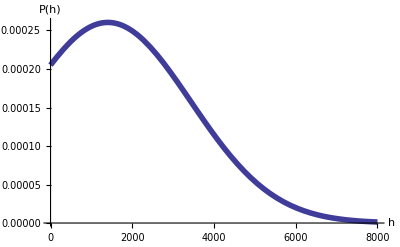

```mathematica
Plot[Ph[100,0.005 * 10,0.1,2805,h],{h,0,8000},PlotRange->All,PlotStyle->Thickness[0.01],BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"h","P(h)"}]
```

If I set some incoming weight threshold θ for a receiving neuron to fire, then the total probability that an h value drawn from the distribution of P(h) is higher than θ is 

f_out = ∫ P(h) dh 

from θ to ∞, which should be some complementary error function erfc().

Then, the average number of receiving neurons that fire would be 
< M_out> = N f_(.08out)
where N is the total number of neurons in the network.  The input connectivity is already accounted for by f_out.

```mathematica
FullSimplify[Integrate[Ph[Nin,R,c,w,h],{h,θ,∞},Assumptions->{Im[θ]==0,Re[θ]>0,Im[h]==0,Re[h]>0,Im[Nin]==0,Re[Nin]>0,Im[R]==0,Re[R]>0,Im[c]==0,Re[c]>0,Re[c]≤1,Im[w]==0,Re[w]>0,Re[1/(c Nin R (-1+(-1+c) R) w^2)]<0}]]
```

(1. ⅇ^(-(3.46945×10^-18 Nin R)/(1.05263+1. R)) √(Nin R (1.05263+1. R)) (0.273153 Abs[-0.05 Nin R w+θ]+(0.0136577 Nin R w-0.273153 θ) Erf[(3.24443 Abs[-0.05 Nin R w+θ])/(√(Nin R (1.05263+1. R)) w)]))/(Abs[-0.05 Nin R w+θ] (0.28025 √(Nin (1.+0.95 R) R)+0.158114 √(Nin R (3.14159+2.98451 R)) Erf[0.223607 √((Nin R)/(2+1.9 R))]))

```mathematica
fout[Nin_,R_,c_,w_,θ_]:=Erfc[(-c Nin R w+θ)/(√2 √(c Nin R (1+R-c R)) w)]/(1+Erf[√((c Nin R)/(2+2 R-2 c R))])
```

```mathematica
fout[400,0.02,0.1,2805,2805]
```

0.507563

```mathematica
SimDataNin = {{40,169.74/1000},{80,288.11/1000},{120,402.1475/1000},{160,507.6/1000},{200,600.2475/1000},{240,653.1225/1000},{280,724.0225/1000},{320,769.1875/1000},{360,815.73/1000},{400,850.9575/1000}};
```

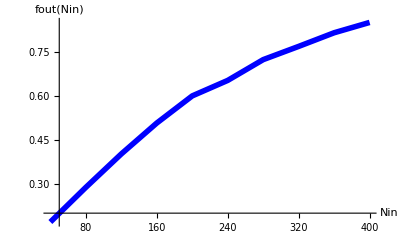

```mathematica
Plot1 = ListPlot[SimDataNin,PlotRange->All,PlotStyle->{Blue,Thickness[0.01]},Joined->True,BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

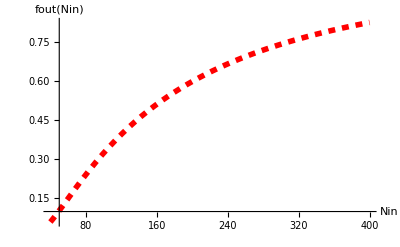

```mathematica
Plot2 = Plot[fout[Nin,0.05 ,0.1,2805,2805],{Nin,40,400},PlotRange->All,PlotStyle->{Red,Dashed,Thickness[0.01]},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

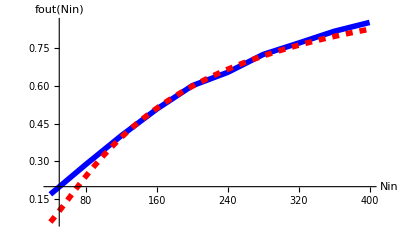

```mathematica
Plot3 = Show[Plot1,Plot2]
```

```mathematica
SimDataC = {{0.05,201.278/1000},{0.1,356.182/1000},{0.15,488.361/1000},{0.2,587.074/1000},{0.25,674.5/1000},{0.3,747.327/1000},{0.35,808.979/1000},{0.4,848.449/1000},{0.45,885.427/1000},{0.5,911.221/1000}};
```

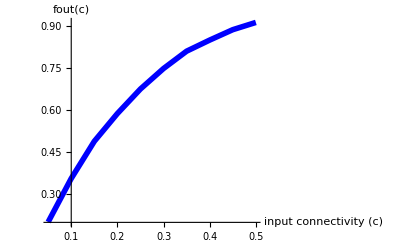

```mathematica
Plot4 = ListPlot[SimDataC,PlotRange->All,PlotStyle->{Blue,Thickness[0.01]},Joined->True,BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"input connectivity (c)","fout(c)"}]
```

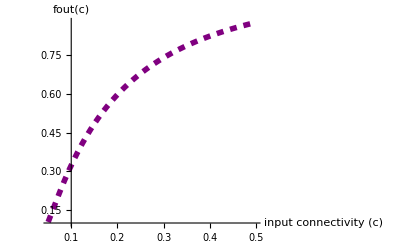

```mathematica
Plot5 = Plot[fout[100,0.05 ,c,2805,2805],{c,0.05,0.5},PlotRange->All,PlotStyle->{Purple,Dashed,Thickness[0.01]},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"input connectivity (c)","fout(c)"}]
```

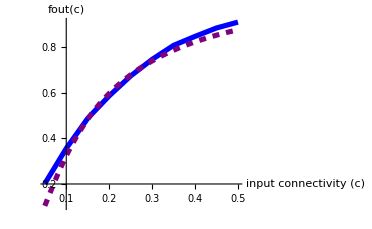

```mathematica
Plot6 = Show[Plot4,Plot5]
```

```mathematica
SimDataR = {{0.02,168.375/1000},{0.04,301.868/1000},{0.06,406.071/1000},{0.08,501.51/1000},{0.1,588.861/1000},{0.12,651.026/1000},{0.14,707.574/1000},{0.16,756.272/1000},{0.18,795.526/1000},{0.2,822.619/1000}};
```

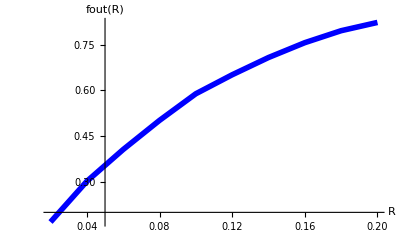

```mathematica
Plot7 = ListPlot[SimDataR,PlotRange->All,PlotStyle->{Blue,Thickness[0.01]},Joined->True,BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"R","fout(R)"}]
```

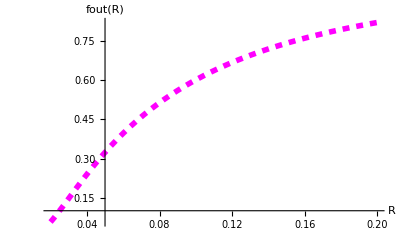

```mathematica
Plot8 = Plot[fout[100,R,0.1,2805,2805],{R,0.02,0.2},PlotRange->All,PlotStyle->{Magenta,Dashed,Thickness[0.01]},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"R","fout(R)"}]
```

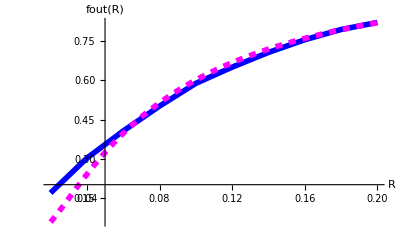

```mathematica
Plot9 = Show[Plot7,Plot8]
```

```mathematica
SimDataNinR4 = {{40,72.434/1000},{80,139.8305/1000},{120,193.4075/1000},{160,248.3775/1000},{200,296.532/1000},{240,348.159/1000},{280,389.7615/1000},{320,435.0915/1000},{360,472.4295/1000},{400,511.658/1000}};
```

```mathematica
SimDataNinR4mult = {{40,74.665/1000},{80,137.4205/1000},{120,199.2075/1000},{160,254.206/1000},{200,306.335/1000},{240,356.777/1000},{280,407.0655/1000},{320,451.5585/1000},{360,506.156/1000},{400,553.9405/1000}};
```

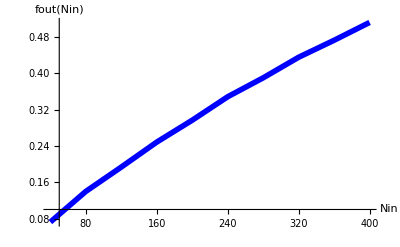

```mathematica
Plot10 = ListPlot[SimDataNinR4,PlotRange->All,PlotStyle->{Blue,Thickness[0.01]},Joined->True,BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

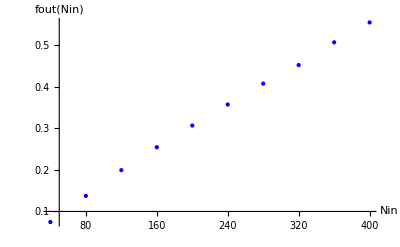

```mathematica
Plot11 =  ListPlot[SimDataNinR4mult,PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.01]},Joined->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

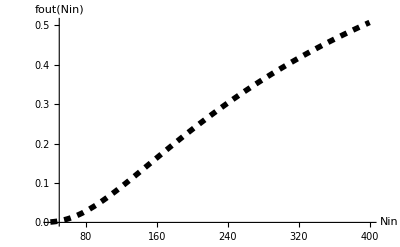

```mathematica
Plot12 = Plot[fout[Nin,0.02 ,0.1,2805,2805],{Nin,40,400},PlotRange->All,PlotStyle->{Black,Dashed,Thickness[0.01]},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

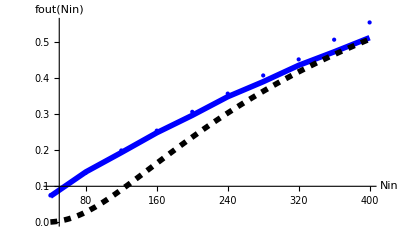

```mathematica
Plot13 = Show[Plot10,Plot11,Plot12]
```

```mathematica
Needs["PlotLegends`"]
```

So, f_out gives the fraction of neurons that fire.  It should be possible to check in simulation whether this f_out is correct.

Let's say a training slice contains N f neurons, where N is the total number of liquid neurons and f is the firing fraction.  Then, to activate all N f neurons via input, the probability is f_out^(N f).  Then, the probability of missing this slice (even by just a little bit) is 1 - f_out^(N f).  Then, the probability of missing all p slices would be ( 1 - f_out^(N f) )^p.  Hence the probability of hitting some slice would be 1 - ( 1 - f_out^(N f) )^p = π (f_out).

Ultimately, the impact of the inputs on the liquid depend on w c λ Δt = w c R.  For starters, this product of w c R should be kept constant when I study f_out, etc.  Then we should explore the impact of introducing variations into w, c or λ.

The question we now ask, is, what are the chances of a particular pattern being excited?  For a very simple model, let's just say that we need a minimum of T neurons in the network to be excited to initiate a replay.  Then, the probability of exciting a replay is

P_min= (f_out^T(1-f_out))^(N-T) 

Of course, we could possibly excite more than T neurons.  So the total probability of our input exciting sequence(s) is

π = P_min + ∑_(L>T) (f_out^(L-T)(1-f_out))^(N-L)((N-T)!)/((N-L)!(L-T)!)

where L goes from T to N.  

Of course, if there are p patterns (slices) stored in the sequence network, then 
1 - .08(1-π)^p = probability that at least one pattern is hit by the input.  This value should be somewhat higher than π (1-π)^(p-1)(p!)/((p-1)!1!), which is the probability of hitting one particular slice and missing all the others.

ProbMin[Nin_,R_,c_,w_,θ_,T_,N_]:=fout[Nin,R,c,w,θ]^T(1-fout[Nin,R,c,w,θ])^(N-T)Binomial[N,T]

ProbPi[Nin_, R_, c_, w_, θ_, T_, N_] := Sum[ProbMin[Nin, R, c, w, θ, L, N], {L, T, N}]

```mathematica
ProbMin[Nin_,R_,c_,w_,θ_,T_,N_]:=fout[Nin,R,c,w,θ]^T(1-fout[Nin,R,c,w,θ])^(N-T)
```

```mathematica
ProbPi[Nin_,R_,c_,w_,θ_,T_,N_]:=ProbMin[Nin,R,c,w,θ,T,N]+Sum[fout[Nin,R,c,w,θ]^(L-T)(1-fout[Nin,R,c,w,θ])^(N-L)Binomial[N-T,N-L],{L,T+1,N}]
```

```mathematica
ProbOne[Nin_,R_,c_,w_,θ_,T_,N_,p_]:= 1 - (1-ProbPi[Nin,R,c,w,θ,T,N])^p
```

```mathematica
ProbPi[100,0.5 10 10^-2,0.1,2805,2805,80,100]
```

0.9996

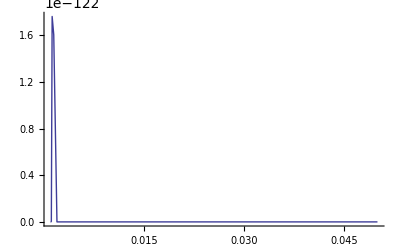

```mathematica
Plot[ProbMin[100,1,c,2805,2805,80,1000],{c,0.001,0.05},PlotRange->All]
```

The function π depends on quite a few variables: π(Nin, R, C, θ, T, N).  We would of course like to pin down a parameter regime that pertains to our simulations.

1. N_in.  This is more or less a free parameter.
2. R.  This is λ Δt, which gives the roughly the number of input spikes per spike train over the duration of Δt.
3. C.  This is c w, where c is the input connectivity and w is the input weight.  
4. θ.  This is the threshold for neuronal firing.  This parameter is empirically fixed to be 3000 pA for my neuronal parameters.
5. T.  The minimum number of neurons that need to be excited for replay.
6. N.  The total number of liquid neurons.

Our goal is to find a regime for C that gives us interesting liquid responses.  So I shall plot the behavior of π as a function of the 4 adjustable parameters N_in, R, T and N.

We shall expore the impact of N first.  One question that needs to be answered is whether π scales with system size.  That is, if I scale all the input parameters with N, would π behave the same?

θ = 2805;
winp = 2805;
wsyn = 2805;
Δt = 0.010;

Ntotal = 1000;

Plot1 = ShowLegend[Plot[{ProbPi[4, 40*0.005, c, winp, θ, 0.3* Ntotal, Ntotal], ProbPi[4, 40*0.005, c, winp, θ , 0.3* Ntotal *2, Ntotal*2 ], ProbPi[4, 40*0.005, c, winp, θ, 0.3 *Ntotal *3, Ntotal *3], ProbPi[4, 40*0.005, c, winp, θ , 0.3 *Ntotal *4, Ntotal *4]}, {c, 0.01, 0.9}, PlotRange -> All, PlotStyle -> {{Thickness[0.01], Green}, {Thickness[0.01], Red}, {Thickness[0.01], Blue}, {Thickness[0.01], Orange}}, BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 20, Thick}, AxesLabel -> {"c", "π"}], {{{Graphics[{Thick, Green, Line[{{0, 0}, {2, 0}}]}], Style["N = 100", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Red, Line[{{0, 0}, {2, 0}}]}], Style["N = 200", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["N = 300", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]},
        {Graphics[{Thick, Orange, Line[{{0, 0}, {2, 0}}]}], Style["N = 400", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}}, LegendPosition -> {1.0, 0.01}, LegendSize -> {1, 0.6}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 18}]

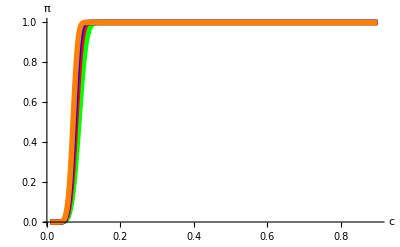

Plot2 = ShowLegend[Plot[{ProbPi[4, 40*0.005, c, winp, θ, 0.3* Ntotal, Ntotal], ProbPi[4, 40*0.005 * 2, c, winp, θ , 0.3* Ntotal *2, Ntotal*2 ], ProbPi[4, 40*0.005 * 3, c, winp, θ, 0.3 *Ntotal *3, Ntotal *3], ProbPi[4, 40*0.005 * 4, c, winp, θ , 0.3 *Ntotal *4, Ntotal *4]}, {c, 0.01, 0.9}, PlotRange -> All, PlotStyle -> {{Thickness[0.01], Green}, {Thickness[0.01], Red}, {Thickness[0.01], Blue}, {Thickness[0.01], Orange}}, BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 20, Thick}, AxesLabel -> {"c", "π"}], {{{Graphics[{Thick, Green, Line[{{0, 0}, {2, 0}}]}], Style["N = 100", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Red, Line[{{0, 0}, {2, 0}}]}], Style["N = 200", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["N = 300", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]},
    {Graphics[{Thick, Orange, Line[{{0, 0}, {2, 0}}]}], Style["N = 400", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}}, LegendPosition -> {1.0, 0.01}, LegendSize -> {1, 0.6}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 18}]

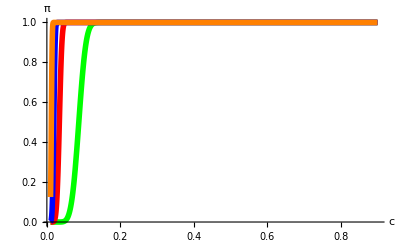

Plot3 = ShowLegend[Plot[{ProbPi[4, 40*0.005, c, winp, θ, 0.3* Ntotal, Ntotal], ProbPi[4*2, 40*0.005, c, winp, θ , 0.3* Ntotal *2, Ntotal*2 ], ProbPi[4*3, 40*0.005, c, winp, θ, 0.3 *Ntotal *3, Ntotal *3], ProbPi[4*4, 40*0.005, c, winp, θ , 0.3 *Ntotal *4, Ntotal *4]}, {c, 0.01, 0.9}, PlotRange -> All, PlotStyle -> {{Thickness[0.01], Green}, {Thickness[0.01], Red}, {Thickness[0.01], Blue}, {Thickness[0.01], Orange}}, BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 20, Thick}, AxesLabel -> {"c", "π"}], {{{Graphics[{Thick, Green, Line[{{0, 0}, {2, 0}}]}], Style["N = 100", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Red, Line[{{0, 0}, {2, 0}}]}], Style["N = 200", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["N = 300", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]},
    {Graphics[{Thick, Orange, Line[{{0, 0}, {2, 0}}]}], Style["N = 400", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}}, LegendPosition -> {1.0, 0.01}, LegendSize -> {1, 0.6}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 18}]

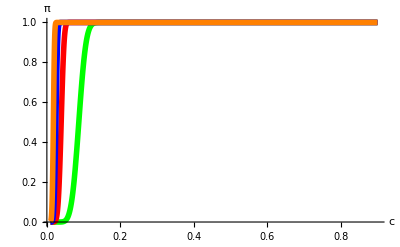

Plot4 = ShowLegend[Plot[{ProbPi[4, 40*0.005, c, winp, θ, 0.3* Ntotal, Ntotal], ProbPi[4, 40*0.005, c, winp, θ , 0.3* Ntotal, Ntotal*2 ], ProbPi[4, 40*0.005, c, winp, θ, 0.3 *Ntotal, Ntotal *3], ProbPi[4, 40*0.005, c, winp, θ , 0.3 *Ntotal, Ntotal *4]}, {c, 0.01, 0.9}, PlotRange -> All, PlotStyle -> {{Thickness[0.01], Green}, {Thickness[0.01], Red}, {Thickness[0.01], Blue}, {Thickness[0.01], Orange}}, BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 20, Thick}, AxesLabel -> {"c", "π"}], {{{Graphics[{Thick, Green, Line[{{0, 0}, {2, 0}}]}], Style["N = 100", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Red, Line[{{0, 0}, {2, 0}}]}], Style["N = 200", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["N = 300", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]},
    {Graphics[{Thick, Orange, Line[{{0, 0}, {2, 0}}]}], Style["N = 400", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}}, LegendPosition -> {1.0, 0.01}, LegendSize -> {1, 0.6}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 18}]

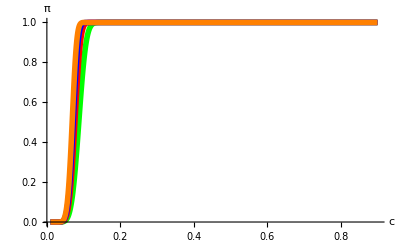

Plot5 = ShowLegend[Plot[{ProbPi[4, 40*0.005, c, winp, θ, 0.3* Ntotal , Ntotal * 4], ProbPi[4, 40*0.005, c, winp, θ , 0.3*Ntotal*2, Ntotal * 4], ProbPi[4, 40*0.005, c, winp, θ, 0.3 *Ntotal*3, Ntotal * 4], ProbPi[4, 40*0.005, c, winp, θ , 0.3 *Ntotal*4, Ntotal *4]}, {c, 0.01, 0.9}, PlotRange -> All, PlotStyle -> {{Thickness[0.01], Green}, {Thickness[0.01], Red}, {Thickness[0.01], Blue}, {Thickness[0.01], Orange}}, BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 20, Thick}, AxesLabel -> {"c", "π"}], {{{Graphics[{Thick, Green, Line[{{0, 0}, {2, 0}}]}], Style["T = 30", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Red, Line[{{0, 0}, {2, 0}}]}], Style["T = 60", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["T = 90", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]},
    {Graphics[{Thick, Orange, Line[{{0, 0}, {2, 0}}]}], Style["T = 120", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}}, LegendPosition -> {1.0, 0.01}, LegendSize -> {1, 0.6}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 18}]

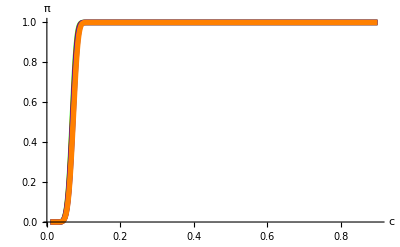

Plot6 = ShowLegend[Plot[{ProbPi[4, 40*0.005, c, winp, θ, 0.3* Ntotal*4 , Ntotal * 4], ProbPi[4, 40*0.005, c, winp*2, θ , 0.3*Ntotal*4, Ntotal * 4], ProbPi[4, 40*0.005, c, winp*3, θ, 0.3 *Ntotal*4, Ntotal * 4], ProbPi[4, 40*0.005, c, winp*4, θ , 0.3 *Ntotal*4, Ntotal *4]}, {c, 0.01, 0.9}, PlotRange -> All, PlotStyle -> {{Thickness[0.01], Green}, {Thickness[0.01], Red}, {Thickness[0.01], Blue}, {Thickness[0.01], Orange}}, BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 20, Thick}, AxesLabel -> {"c", "π"}], {{{Graphics[{Thick, Green, Line[{{0, 0}, {2, 0}}]}], Style["winp = θ", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Red, Line[{{0, 0}, {2, 0}}]}], Style["winp = 2θ", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["winp = 3θ", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]},
    {Graphics[{Thick, Orange, Line[{{0, 0}, {2, 0}}]}], Style["winp = 4θ", {FontFamily -> "Helvetica", FontSize -> 20, Thick}]}}, LegendPosition -> {1.0, 0.01}, LegendSize -> {1, 0.6}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 18}]

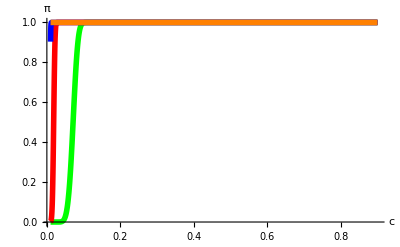

-----------------------------------------------------------------------------------------------------------------------------

So the lesson so far is, to get a nicely smooth "transition" from non-firing to all-firing, we want low-input rate/low input number, and a high value of T.

Also, on must keep in mind that, the probability sampled here is the over a time span of Δt.  That means, if we run a simul

Plot9 = Plot[ProbPi[4, 100 * Δt, c, θ, θ, 80, 100], {c, 0.01, 0.99}, PlotRange -> All, PlotStyle -> {Thickness[0.01], Orange}, BaseStyle -> {FontFamily -> "Helvetica", FontSize -> 20, Thick}, AxesLabel -> {"c", "π"}, PlotRange -> All]

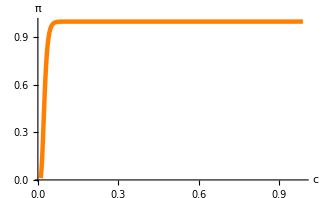

```mathematica
2805 / 50//N
```

56.1

# The Impact of Synaptic Weights

So in my simulations, I tested the sequence network with one initial pulse to every single network neuron, at exactly the same time, with just enough input weight θ to make the neurons fire once.  The purpose is to observe the resulting network response as a function of the inter-neuronal synaptic weight.

What I found was that, if I scale the synaptic weight by 1/(N f), where N is the total number of neurons and f is the fraction of N that I require to fire in every training "slice", then it's pretty much guanranteed that there would be a sequence replay.  On the other hand, if I set the synaptic weight to be 1/(N c), where c is the average number of post-synaptic neurons each pre-synaptic neuron is connected to, then there is NO sequnce replay.  Bear in mind that c = 1 - e^(-R f^2)and we require c > f, by having a large enough R (pairs of patterns).

However, if I up the synaptic weight to be w ~ 1/(0.9 N c), then the sequence replay become very common again, and the transition from one regime to another is quite abrupt.

So I want to understand this a little more.  More specifically, I suspect there are

It's fair to say that the value of T and the synaptic weight are intricately related.  The value of T, for my purpose, is the minimum number of liquid neurons that need to be excited by the input to initiate

So if I want to really test the probability of ONE input pulse

Testing my stuff

So here are some notes suggested by Christian:

suppose the patterns (slices) I store in the system are annotated by the variable "a", with a = 1, 2......ϕ, then the following equations describe the time evolution of the memory traces of these slices:

m_α(t + Δt) = m_α(t) e^(-Δt/τ) + J_α(t), where m_α is the variable describing the state of prevalence of pattern α, τ is some decay time constant I must reasonably, and J_α(t) is the number of neurons of pattern α firing at time t.  "This is essentially a low-pass filter".

As for the entire network, 
n(t+Δt) = n(t)e^(-Δt/τ) + K(t) , where K(t) is the number of neurons of the entire network firing at t.

Then the variable V_α(t) that determines the prominence of a particular pattern at time t is
m_α/M_α - n/N = V_a(t), where M is the total number of firing neurons stored in pattern α.

So what can I do with this?

Ultimately, what I care about is how to generate sequence replays with randomized inputs.  If I artificially excite the first of the training slices, I observe 

So the patterns go in color order of: Blue, Green, Red, Aqua, Magenta, etc....

Why is my first slice (Blue) always so subdued after the initial kick?  It's because the way we set up the sequences denies the first slice to be feed-forwardly connected by any other slice.  That's not saying the neurons in the first slice are not connected to by other neurons.  In fact, during the pattern construction, it's entirely possible that some neurons in the first slice, or perhaps even all of them, would become parts of other slices.  But because these neurons are connected to separately by the other slices, they're not all activated at the same time, and hence we observe very little overall activity of the first slice as time moves on.

Of course, my goal is to ultimately set up randomized inputs that would SOMETIMES excite sequence replays, but most of the time displaying input-driven decays.  How should this be carried out?

It might be best to have multiple Poisson input trains, each one connectived to a fraction of the network neurons.  The input weights should be large enough such that each input spike would induce a spike.  This brings us back to the previous derivations.

So I've set my synaptic weights θ such that I'd need to activate all M "on" neurons of a slice to trigger a sequence replay.  This way, the probability for the input to trigger a sequence becomes:

P_min=1-(1-f_out^M)^Pn,

where f_out is the probability for the input to excite a particular network neuron, M is the number of "on" neurons per slice, and Pn is the number of slices in the training.

```mathematica
ProbMin3[Nin_,R_,c_,w_,θ_,M_,Pn_]:=1-(1-fout[Nin,R,c,w,θ]^M)^Pn
```

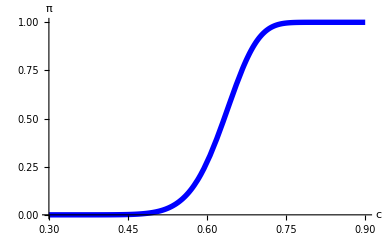

```mathematica
Plot[ProbMin3[5,20,c,2805/30,2805,30,6],{c,0.3,0.9},PlotRange->All,PlotStyle->{Thickness[0.01],Blue},BaseStyle->{FontFamily->"Helvetica",FontSize->25,Thick},AxesLabel->{"c","π"}]
```

```mathematica
2805/165//N
```

17.

Some Suggestions

1.) Input connect to all neurons, not just exc. ones.

2.) Inh. neurons should comprise ~20% of the network.

3.) Lower the exc. --> inh. weights, while increasing the inh. --> exc. weights.

4.) Maybe smaller M?

Christian's New Derivation for Input-driven Firing

h  = w ∑ s_i, where the summation goes from i = 1 to i = c N_in, where c is input connectivity and N_in is the number of inputs.  w is the constant input synaptic weight.

Take R = λ dt, where λ is the average input spike rate and dt is the time bin for one spike.

p(s) then has 2 states: p(s) = R for s = 1, and 1-R for s = 0
(for a Poisson process, e^(-λ dt) is the probability of not spiking over dt.  In the limit of small λ dt, e^(-λ dt) ~ 1 - λ dt = 1 - R.  The probability of spiking is hence R.)

f_out is the probability that of h >= θ, where θ is the threshold.

So the probability of a neuron receiving exactly x spikes is the following:
p( x spikes ) = R^x (1-R)^(N_in c - x) Binomial[N_in c, x].

Then

f_out = ∑ p( x spikes ), where the summation goes from x >= θ/w to N_in c

f_out could be an "Incomplete Beta Function"

Let's see if this derivation works better than the previous one.

```mathematica
px[Nin_,R_,c_,x_]:= (1-Exp[-R])^x(Exp[-R])^(Nin c - x)Binomial[Nin c,x]
```

```mathematica
foutcl[Nin_,R_,c_,w_,θ_]:= Sum[px[Nin,R,c,x],{x,θ/w,100}]
```

CW's New Derivation for Input-driven Firing

Let's say I have exactly N_in inputs.  Each one is a Poisson spike train with average rate of λ.  Each network neuron receives N_in * c inputs.  Because the Poisson spike trains are independent, we may sum their rates to give rise to one total arrival process:
P(s) = ((e^(-N_in c R)(N_in c R))^s)/(s!)
which is the probability of having s arrivals within a time span of dt, with R = λ dt.  

If the weights from the input spikes are the same (w), then the probability of a neuron receiving a particular weight over the time span of dt is

Pw = P(θ/w)

```mathematica
Ps[Nin_,R_,c_,s_]:= (ⅇ^(-Nin c R) (Nin c R)^s)/(s!)
```

where the firing threshold of a network neuron is θ.  Then the probability of a network neuron firing is (note the normalization):

```mathematica
Pout[Nin_,R_,c_,w_,θ_]:=Integrate[Ps[Nin,R,c,s],{s,θ/w,∞}]/Integrate[Ps[Nin,R,c,s],{s,0,∞}]
```

```mathematica
Pout[40,0.02,0.1,2805,2805]//N
```

0.0612098

```mathematica
fout[400,0.02,0.1,2805,2805]
```

0.507563

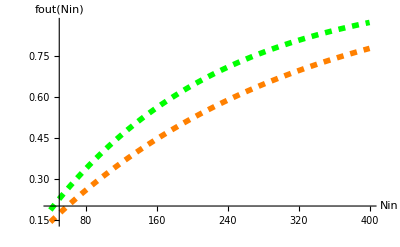

```mathematica
Plot22 = Plot[{foutcl[Nin,0.05,0.1,2805,2805],Pout[Nin,0.05 ,0.1,2805,2805]},{Nin,40,400},PlotRange->All,PlotStyle->{{Dashed,Green,Thickness[0.01]},{Dashed,Orange,Thickness[0.01]}},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

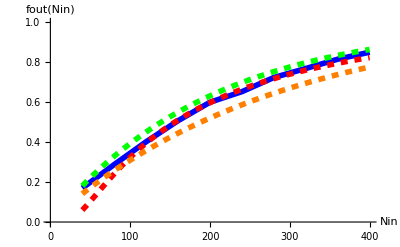

```mathematica
PlotNin = Show[{Plot1,Plot2,Plot22},AxesOrigin->{0,0},PlotRange->{{0,400},{0,1}},BaseStyle->{FontFamily->"Helvetica",FontSize->16,Thick}]
```

```mathematica
PlotNinLeg = ShowLegend[PlotNin,{{{Graphics[{Thick, Green,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CL's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["simulation", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Red,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["old theory", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]},
    {Graphics[{Thick, Orange,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CW's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}}, LegendPosition -> {0.75, 0.01}, LegendSize -> {1, 0.6}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 18}]
```

-Graphics-

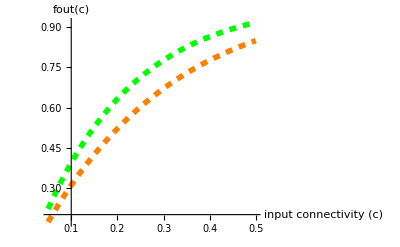

```mathematica
Plot25 = Plot[{foutcl[100,0.05,c,2805,2805],Pout[100,0.05 ,c,2805,2805]},{c,0.05,0.5},PlotRange->All,PlotStyle->{{Green,Dashed,Thickness[0.01]},{Orange,Dashed,Thickness[0.01]}},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"input connectivity (c)","fout(c)"}]
```

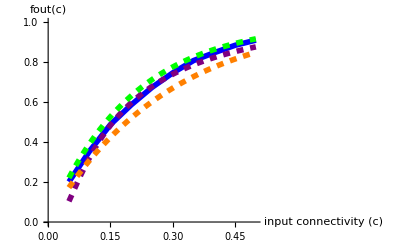

```mathematica
PlotInput = Show[{Plot4,Plot5,Plot25},AxesOrigin->{0,0},PlotRange->{{0,0.5},{0,1}},BaseStyle->{FontFamily->"Helvetica",FontSize->12,Thick}]
```

```mathematica
PlotInputLeg = ShowLegend[PlotInput,{{{Graphics[{Thick, Green,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CL's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["simulation", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Purple,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["old theory", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]},
    {Graphics[{Thick, Orange,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CW's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}}, LegendPosition -> {0.4, -0.2}, LegendSize -> {0.5, 0.4}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 12}]
```

-Graphics-

```mathematica
Export["/Users/CW/Desktop/Comparison_Input.pdf",PlotInputLeg,"PDF","EmbeddedFonts"->False]
```

/Users/CW/Desktop/Comparison_Input.pdf

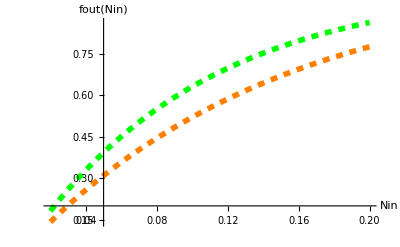

```mathematica
Plot28 = Plot[{foutcl[100,R,0.1,2805,2805],Pout[100,R,0.1,2805,2805]},{R,0.02,0.2},PlotRange->All,PlotStyle->{{Green,Dashed,Thickness[0.01]},{Orange,Dashed,Thickness[0.01]}},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

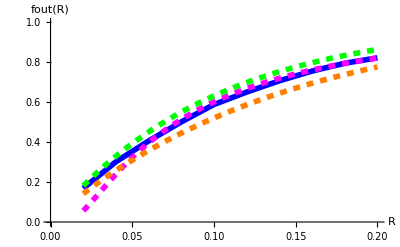

```mathematica
PlotR = Show[{Plot7,Plot8,Plot28},AxesOrigin->{0,0},PlotRange->{{0,0.2},{0,1}},BaseStyle->{FontFamily->"Helvetica",FontSize->16,Thick}]
```

```mathematica
PlotRLeg =ShowLegend[PlotR,{{{Graphics[{Thick, Green,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CL's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["simulation", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Magenta,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["old theory", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]},
    {Graphics[{Thick, Orange,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CW's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}}, LegendPosition -> {0.6, -0.3}, LegendSize -> {0.6, 0.4}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 12}]
```

-Graphics-

```mathematica
Export["/Users/CW/Desktop/Comparison_R.pdf",PlotRLeg,"PDF","EmbeddedFonts"->False]
```

/Users/CW/Desktop/Comparison_R.pdf

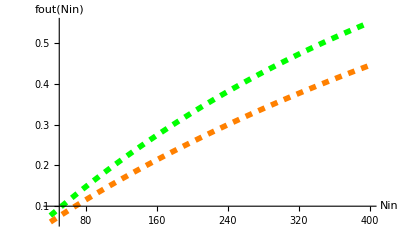

```mathematica
Plot32 = Plot[{foutcl[Nin,0.02,0.1,2805,2805],Pout[Nin,0.02 ,0.1,2805,2805]},{Nin,40,400},PlotRange->All,PlotStyle->{{Green,Dashed,Thickness[0.01]},{Orange,Dashed,Thickness[0.01]}},BaseStyle->{FontFamily->"Helvetica",FontSize->18,Thick},AxesLabel->{"Nin","fout(Nin)"}]
```

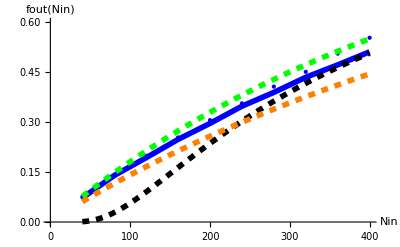

```mathematica
PlotNin2 = Show[{Plot10,Plot11,Plot12,Plot32},AxesOrigin->{0,0},PlotRange->{{0,400},{0,0.6}},BaseStyle->{FontFamily->"Helvetica",FontSize->16,Thick}]
```

```mathematica
PlotNin2Leg = ShowLegend[PlotNin2,{{{Graphics[{Thick, Green,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CL's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]},{Graphics[{Thick, Blue,Dotted, Line[{{0, 0}, {2, 0}}]}], Style["sim., mult./bin", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Blue, Line[{{0, 0}, {2, 0}}]}], Style["sim., max 1/bin", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}, {Graphics[{Thick, Black,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["old theory", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]},
    {Graphics[{Thick, Orange,Dashed, Line[{{0, 0}, {2, 0}}]}], Style["CW's new", {FontFamily -> "Helvetica", FontSize -> 12, Thick}]}}, LegendPosition -> {0.6, -0.4}, LegendSize -> {1.0, 0.5}, LegendShadow -> None, LegendBorder -> None, LegendTextOffset -> Automatic}, LabelStyle -> {FontFamily -> "Helvetica", FontSize -> 20}]
```

-Graphics-

```mathematica
Export["/Users/CW/Desktop/Comparison_Nin2.pdf",PlotNin2Leg,"PDF","EmbeddedFonts"->False]
```

/Users/CW/Desktop/Comparison_Nin2.pdf

Derivation for Input-driven Firing

```mathematica
Needs["PlotLegends`"]
```

Now that we have a good idea of how f_out works, let's move onto the analysis on input-triggered reply.

Let's imagine we set up our network such that we have p replay slices (or subgroups, whatever you want to call them).  Each slice contains exactly N f neurons, where N is the total number of liquid neurons and f is the firing fraction.  Let's further assume that these slices are not overlapping.  We connect only these slices to each other, in a periodic sequence, such that triggering any single one of them would initiate a replay.

To activate exactly all N f neurons via input, the probability is f_out^(N f).  Then, the probability to NOT activitate all N f neurons of this slice (effectively missing it) is 1 - f_out^(N f).  

Let's say there are p slices embedded in the network.  
Then, the probability of missing all p slices would be ( 1 - f_out^(N f) )^p.  Hence the probability of hitting some slice would be 1 - ( 1 - f_out^(N f) )^p = π (f_out).

The challenge now is how to set up a NEST simulation that tests this function π.  The problem arises from the propagation of the sequence, which complicates the data analysis because those replays are not triggered by the inputs.  How does one filter out the replays intrinsic to the network?  Incorporating inhibitory neurons might work, but it will also introduce effects not accounted for by the simple theory mentioned above.

```mathematica
πCL[Nin_,R_,c_,w_,θ_,N_,f_,p_]:=1 - ( 1 - foutcl[Nin,R,c,w,θ]^(N f))^p
```

```mathematica
πCW[Nin_,R_,c_,w_,θ_,N_,f_,p_]:= 1 - ( 1 - Pout[Nin,R,c,w,θ]^(N f))^p
```

Notes on whta to do with super-weight network

Here are some notes on what to do to characterize the super-weight network behavior:

1. PCA analysis.  Only look at, say, the top 30 eigenvalues/eigenvectors.
2. Look at the susceptibility to input jitter.
3. Look at ISI (inter-spike interval?) firing of individual neurons.
4. Look at how Brunel (2000) or Mehring (2003) characterize/quantify these things.
5. Look into using Support Vector Machine to perform classification.

6. To understand the dynamics of the system better, try injecting a current pulse (delta function, square function etc.) into all network neurons simultaneously, and see how the dynamics decays away

7. Look at how the psth bin size impacts the "performance vs. time" plots.

8. Jitter the input slightly to see if the results change.  That means you train the weights (using svm, perceptron, whatever) using the original inputs, then you test the accuracy using the jittered inputs.  The 2nd test would be, for each iteration of the training, you train with a slightly jittered version.

Find where the network and the input susceptibility to jitter cross in performance.

9. Try injecting a current pulse to only a subset of the network to see what happens.  Obtain firing rate as a function of time for these 1-shot simulations.  Look at raster plots around the w=500k performance peak.

10. For autocorrelation analysis, collapse all neurons into one temporal pattern, and then look at the autocorrelation of this 1-D spike time series.  The dominant frequency should show up as the peak.

11. introduce a Gaussian kernel to every spike before binning, to create a more smoth psth curve, before performing Fourier Transform.

12.  Use the Fourier Transform Analysis to obtain power density spectra, for both the distributed-connectivity and the constant-number-connectivity case, around the "critical point" of 482k synaptic weight.

13. Go into the membrane dynamics to see if you could explain the oscillatory behavior and the network's sensitivity to input jitter.  Also, use finer NEST resolution (0.01ms or smaller, as supposed to 0.1ms).

14. Try smaller input weight.

15. Remove psc memory

16. Check your numerics, including data binning, etc.  Compare the psth vectors of the low resolution case (1e-1 ms) and high resolution case(1e-3 ms).  See if these vectors are very different.

Restart

1. Construct a network of inhibitory neurons.  The population would consist of two types of inhibitory neurons, different by their oscillatory firing rate.  All neurons are connected to each other.

The input to this network would be random, with strong weight.  The input synapses would carry long time constants, such that it would really drive the system.

Then, test this network with the same old classification procedure.

2. Go back and look at the synfire w/ inhibition network and see what can be done with it.